```mathematica
ρ1[x_,rx_,ry_,n_]:=ry (1-Abs[x/rx]^n)^(1/n)
ρ2[x_,rx_,ry_,n_]:=-ry (1-Abs[x/rx]^n)^(1/n)
```

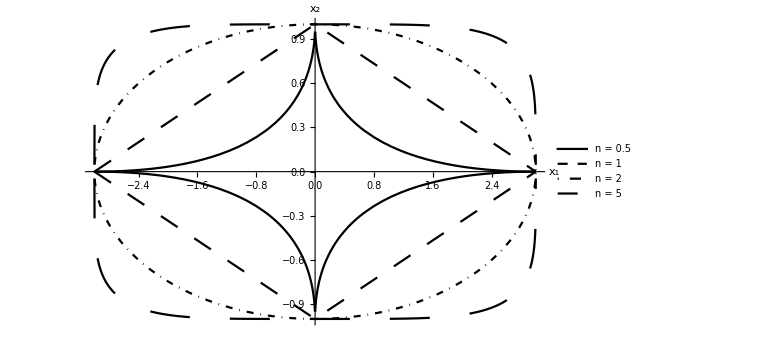

```mathematica
Plot[{ρ1[x,3,1,0.5],ρ1[x,3,1,1],ρ1[x,3,1,2],ρ1[x,3,1,5],ρ2[x,3,1,0.5],ρ2[x,3,1,1],ρ2[x,3,1,2],ρ2[x,3,1,5]},{x,-3,3},PlotRange->All,ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"x_1","x_2"},PlotStyle->{Black,{Black,Dashing[0.025]},{Black,DotDashed},{Black,Dashing[0.05]}},PlotLegends->{"n = 0.5", "n = 1", "n = 2", "n = 5"}]
```

```mathematica
ρ[x_,y_,rx_,ry_,n_]:=(Abs[x/rx]^n+Abs[y/ry]^n)^(1/n)
ϕ[x_,y_,p_,q_,rx_,ry_,n_]:=Piecewise[{{(p n)/(4rx ry Beta[1/n,1/n] Beta[2/p,q+1])(1-(Abs[x/rx]^n+Abs[y/ry]^n)^(p/n))^q, Abs[x/rx]^n+Abs[y/ry]^n≤1}, {0, Abs[x/rx]^n+Abs[y/ry]^n>1}}]
```